{{0.0239927,0.00420587},{0.00420587,0.0389597}}

Fields at upperLimit: 0.261756

Relation at upperLimit: {15.9906-1.37676×10^-13 ⅈ}

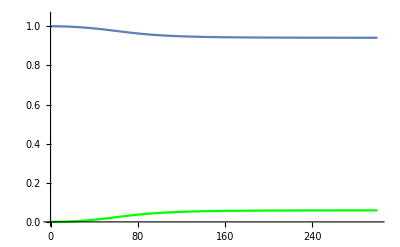

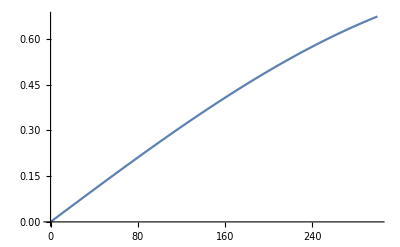

```mathematica
Clear["Global`*"]
BSurf:=1.5*10^13;
R0:=10;
angleIteration:=Pi/6;
bRep:={bRad->0,
	bTheta->0.5*BSurf*Sin[angleIteration]*(R0/(z+R0))^3,
(*bPhi->0.1};*)
bPhi->0.2 BSurf*Sin[z/upperLimit]*(R0/(z+R0))^3};
	(*bPhi->BSurf*Cos[angleIteration]*(R0/(z+R0))^3};*)
(*0.5*BSurf*Sin[angleIteration]*(R0/(z+R0))^3*)
Bcrit:=4.4*10^13;
alpha:=1/137;

k0:=10*5.06*10^9;
(*eV*5.06*10^9*)

(*Убрал ⅈ!*)
mat:=k0 delta/2 {{M,P},{P,n}};
B:={bPhi,bTheta,bRad};
Bunit:=B/Norm[B];

M:=((7 Bunit[[1]]^2 + 4 Bunit[[2]]^2)*μ[[1,1]] - 12 delta* Bunit[[1]]^2*Bunit[[2]]^2)/(μ[[1,1]]*μ[[2,2]]-16 delta^2 *Bunit[[1]]^2*Bunit[[2]]^2);
n:=((4 Bunit[[1]]^2 + 7 Bunit[[2]]^2)*μ[[2,2]] - 12 delta* Bunit[[1]]^2*Bunit[[2]]^2)/(μ[[1,1]]*μ[[2,2]]-16 delta^2 *Bunit[[1]]^2*Bunit[[2]]^2);
P:=(3μ[[1,1]]-4 delta (4 Bunit[[1]]^2 + 7 Bunit[[2]]^2))*Bunit[[1]]*Bunit[[2]]/
(μ[[1,1]]*μ[[2,2]]-16 delta^2 *Bunit[[1]]^2*Bunit[[2]]^2);

delta:=alpha/(45 Pi)*(Norm[B]^2/Bcrit^2);

Bmatrix:=Transpose[{B}].{B}/Norm[B]^2;
beta:=Norm[B]/Bcrit;

μ:=(1+a)*IdentityMatrix[3]+m *Bmatrix;
(*a:=-2 alpha/(45 Pi)*beta^2;
m:=-4 alpha/(45 Pi)*beta^2;*)

a:=-2 alpha/(9 Pi)*Log[1+beta^2*(1+0.25487*beta^(3/4))/(5*(1+0.75*beta^(5/4)))];
m:=-alpha/(3Pi)*beta^2/(3.75+2.7*beta^(5/4)+beta^2);

Amat[z_]:={{Axx[z],Axy[z]},{Ayx[z],Ayy[z]}};
Amat0:={{Axx[0]==1,Axy[0]==0},{Ayx[0]==0,Ayy[0]==0}};

upperLimit:=300;
eqs=NDSolve[Join[{ⅈ Amat'[z]==-Amat[z].mat+ConjugateTranspose[mat].Amat[z]/.bRep},Amat0],{Axx[z],Ayy[z]},{z,0,upperLimit}];

Print[mat/.bRep/.z->100];
Print["Fields at upperLimit: ",(bPhi/bTheta)/.bRep/.z->100];
Print["Relation at upperLimit: ",(Axx[z]/Ayy[z])/.eqs/.z->upperLimit];
p1=Plot[Re[Evaluate[{Axx[z]}/.eqs]],{z,0,upperLimit},PlotRange->{{0,upperLimit},{0.0,1.05}}];
p2=Plot[Re[Evaluate[{Ayy[z]}/.eqs]],{z,0,upperLimit},PlotRange->{{0,upperLimit},{0.0,1.05}},PlotStyle->Green];
Show[p1,p2]
p3=Plot[(bPhi/bTheta)/.bRep,{z,0,upperLimit}]
```